# CS 478

## Scott Leland Crossen

## Backpropagation Project

### Part 1

The code that implements the backpropagation rule is included with the submission of this project. It is written in Scala and follows the functional paradigm. Immutability is observed in all but the underlying learner.

### Part 2

In order to show the full shape of the graph, the stopping criteria for this part was defined to be 10 successive epochs without improvement beyond the minimum mean squared error. In this case, the stopping criteria was met after 106 epochs (a total of .35 seconds). The final accuracy for this 75/25 training/testing split was 0.9904761904761905 on the training set and 0.9333333333333333 on the testing set.

It is noteworthy to point out how the data shows a discrete layer-nature in the accuracy plots. I attribute this to two main reason. The first is machine precision. The calculation for accuracy is computed over a fixed number of rows for which the output of each is either a “1” (classified correctly) or “0” (classified incorrectly). Because of the discrete and limited nature of the accuracy calculation it is very likely that discrete features will be seen in the graphical representation of the data. Moreover, the accuracy is an emergent behavior of the various weights that compose the neural net. At some point the neural net modifies it’s weights to overcome a threshold where it starts to classify things correctly. The speed for which this threshold is met is determined by the learning rate. At this point the algorithm stops classifying things with random probability and starts classifying correctly. This threshold is another possible reason for the discrete nature of the displayed accuracy plots.

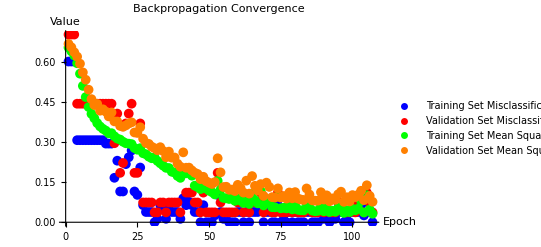

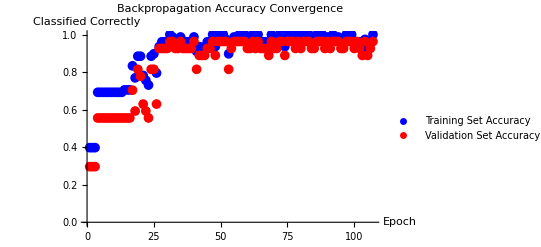

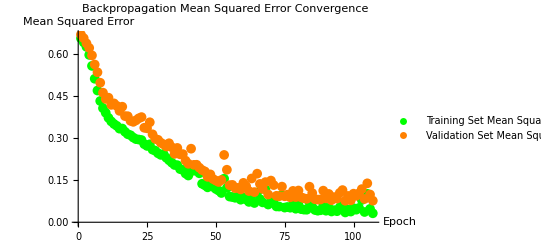

```mathematica
trainingSetAccuracies = {0.3974358974358974,0.3974358974358974,0.3974358974358974,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.6923076923076923,0.7051282051282052,0.7051282051282052,0.7051282051282052,0.8333333333333334,0.7692307692307693,0.8846153846153846,0.8846153846153846,0.782051282051282,0.7564102564102564,0.7307692307692307,0.8846153846153846,0.8974358974358975,0.7948717948717948,0.9358974358974359,0.9615384615384616,0.9615384615384616,0.9615384615384616,1.0,0.9871794871794872,0.9358974358974359,0.9487179487179487,0.9871794871794872,0.9358974358974359,0.9615384615384616,0.9615384615384616,0.9615384615384616,0.9871794871794872,0.9102564102564102,0.9358974358974359,0.9230769230769231,0.9358974358974359,0.9615384615384616,0.9615384615384616,1.0,0.9358974358974359,1.0,1.0,1.0,0.9743589743589743,0.8974358974358975,0.9615384615384616,0.9871794871794872,0.9743589743589743,1.0,1.0,1.0,0.9615384615384616,0.9615384615384616,1.0,0.9615384615384616,1.0,0.9615384615384616,0.9615384615384616,0.9615384615384616,0.9230769230769231,1.0,0.9615384615384616,0.9615384615384616,1.0,1.0,0.9358974358974359,1.0,0.9743589743589743,1.0,0.9615384615384616,1.0,0.9615384615384616,1.0,1.0,1.0,0.9615384615384616,0.9615384615384616,1.0,1.0,1.0,0.9615384615384616,0.9871794871794872,0.9615384615384616,1.0,0.9743589743589743,0.9871794871794872,0.9615384615384616,0.9615384615384616,1.0,0.9743589743589743,1.0,0.9615384615384616,0.9615384615384616,0.9615384615384616,0.9358974358974359,0.9743589743589743,0.9230769230769231,0.9615384615384616,1.0};
validationSetAccuracies = {0.2962962962962963,0.2962962962962963,0.2962962962962963,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.5555555555555556,0.7037037037037037,0.5925925925925926,0.8148148148148148,0.7777777777777778,0.6296296296296297,0.5925925925925926,0.5555555555555556,0.8148148148148148,0.8148148148148148,0.6296296296296297,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.8148148148148148,0.8888888888888888,0.8888888888888888,0.8888888888888888,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.8888888888888888,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.8148148148148148,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9259259259259259,0.8888888888888888,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.8888888888888888,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9259259259259259,0.9629629629629629,0.9629629629629629,0.9629629629629629,0.9259259259259259,0.9629629629629629,0.9259259259259259,0.8888888888888888,0.9629629629629629,0.8888888888888888,0.9259259259259259,0.9629629629629629};
trainingSetMse = {0.6552342423640292,0.6408325543950788,0.6249970155506919,0.5961843492992015,0.5569661074609347,0.5112211117424879,0.4692940462649557,0.4319777133044221,0.406263206447426,0.3898466997439498,0.3718614034132175,0.3592506294818036,0.35015131216194323,0.34347196398765495,0.3334433311687151,0.33391225401610874,0.32236986561553466,0.3136940996026338,0.30998251672930005,0.30178181550812766,0.29614397933524395,0.294603628276002,0.2928435954327163,0.2781751869020167,0.27196984417525927,0.2777205086842186,0.25872090196648595,0.2548391062458521,0.24578529366876473,0.24002781555045602,0.2431622245428669,0.2297525656696203,0.2209197368151618,0.21220068118513447,0.20404890123427105,0.20328991269747015,0.18934600188532102,0.18623074567591202,0.1736450653505924,0.16648513863207204,0.18756627498997974,0.18355366633172185,0.18865932094146667,0.17446612492181726,0.13706179786381661,0.1317805940234114,0.12439764084531926,0.14799960761782047,0.12627833691496199,0.1186051497550627,0.11287701162811586,0.10422109582212652,0.15525465394093835,0.12216422670913506,0.09150918136799036,0.0898526038162242,0.08722016864294241,0.09164905280049397,0.0803191964659962,0.08894495043292368,0.08119202359347849,0.07251953830250872,0.09619216240875236,0.06860327307616686,0.10595300428806631,0.08231810267260006,0.07079479116970851,0.11734881160170471,0.06317343705416899,0.08810882112654984,0.07753407111560928,0.056325032236430934,0.0559207402499614,0.09729490077204546,0.05223505200686057,0.054386002057460046,0.051856740148711555,0.061584927376159,0.04820491888390029,0.061811408145383724,0.0466933968777776,0.04504899661136008,0.04466552915389915,0.07027807346804667,0.05475353622944006,0.04369481913263928,0.04119605472427659,0.042769188355520585,0.059631009668108824,0.04115358729148645,0.05102547109142463,0.038379067019753625,0.0430727487294689,0.03943949531049421,0.05333022500115838,0.06014943578441246,0.03497206695710427,0.04498848082782567,0.038107045911182025,0.050231811973668106,0.044813552461209015,0.051194373039814126,0.07930255959738142,0.03656451191823308,0.10124386696466808,0.047692584317987306,0.03195500913062534};
validationSetMse = {0.6686474191835949,0.6557840431343953,0.6372566764419858,0.6209663489780133,0.5944675663781497,0.561825515877718,0.5343168398247629,0.49700161390277925,0.4615941510128583,0.43922219488416386,0.44374057366048564,0.4182105284728457,0.4235009385334716,0.4146014278055962,0.3968611009608179,0.41160506057212415,0.3781307544531358,0.3776984513593004,0.3612365180224738,0.3576761356076088,0.3631195682935622,0.370235282279283,0.37455104044569093,0.33659703492037824,0.3348084439848566,0.3561747928664723,0.31320787510185283,0.29719254699423675,0.2936617622754136,0.28314764513462737,0.27764384217274385,0.2697841099277731,0.28138098811267104,0.2669877137565196,0.24360442762413068,0.26474562049224515,0.24197381334443627,0.2427002909027579,0.21950750747233483,0.20823234711520747,0.2620651495511065,0.20444738374253354,0.20480953369851845,0.19433050299072308,0.1858237749486254,0.18110443713777993,0.16168437685953604,0.17046116154113913,0.15392492652783285,0.14838235833093275,0.14345905093065062,0.1504851644320455,0.2397775887838155,0.18701300080358094,0.131959983586604,0.13303930241610348,0.12170800016345762,0.12247022120156587,0.11695783926325334,0.14028458052138223,0.1283414076441494,0.11109206040139864,0.15591540808366336,0.10741695393170946,0.1730806607362933,0.13657036103459166,0.11859740446532799,0.14294959858007256,0.09892379027380287,0.14847433440851004,0.13242671814196785,0.09412462514401267,0.09279077494793037,0.12689100637794,0.09259480889956848,0.09836597357485827,0.08890102151594609,0.11169399176477708,0.08968971476000538,0.11301370621819942,0.08877557594228823,0.0852386640219342,0.08351214403494868,0.12670524330644076,0.10405290982276366,0.08212690183520038,0.08075827193389465,0.08109481708315529,0.11256304280913484,0.08518609112124842,0.10088469469475442,0.07863360254895334,0.08950103923907005,0.08425622829337398,0.10472857043788703,0.11457009983644605,0.07655436385138993,0.09373728302264087,0.0781314166547198,0.10180021336823504,0.09421506050961997,0.10307165033903505,0.1180377294419575,0.08292056397157233,0.13867913251526387,0.09880917624373617,0.07679263059027847};
range = Range[Length[trainingSetAccuracies]];

ListPlot[{Transpose[{range,1-trainingSetAccuracies}],Transpose[{range,1-validationSetAccuracies}],Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}]}, AxesLabel->{Style["Epoch", Black],Style["Value", Black]}, PlotLabel->Style["Backpropagation Convergence", Black], PlotStyle->{Blue, Red, Green, Orange},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Misclassification", "Validation Set Misclassification","Training Set Mean Squared Error", "Validation Set Mean Squared Error"}]

ListPlot[{Transpose[{range,trainingSetAccuracies}],Transpose[{range,validationSetAccuracies}]}, AxesLabel->{Style["Epoch", Black],Style["Classified Correctly", Black]}, PlotLabel->Style["Backpropagation Accuracy Convergence", Black], PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Validation Set Accuracy"}]

ListPlot[{Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}]}, AxesLabel->{Style["Epoch", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["Backpropagation Mean Squared Error Convergence", Black], PlotStyle->{Green, Orange},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Mean Squared Error", "Validation Set Mean Squared Error"}]
```

### Part 3

To understand a good baseline, I first ran the vowels data set on the “baseline learner” and the perceptron. the reported accuracy for these two algorithms were 0.068 and 0.25 respectively. Out of the box, the backpropagation algorithm had a test-set accuracy of 0.72 which is significantly better.

Upon looking at the data set it is obvious that many of the features are redundant or extraneous. For example, whenever the name “Andrew” appears, it is followed with the fact that he is a man. The same goes with every other name included in the file. The third column therefore is not needed. Moreover, the first column is also an extraneous features. Names included in “Train” are not included in “Test” and vice-versa. The second column is the only column of the first three that actually holds all information by itself. The first and second are not needed. If these columns were included it would be likely that neural net would put their weights effectively to zero anyway.

Below are the plots showing convergence vs learning rate. As shown, all metrics converge at around a learning rate of ten. I attribute this to the fact that learning rates above this value adhere to a law of diminishing returns that make increase in learning rate less viable.

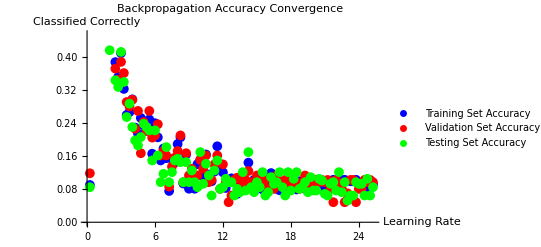

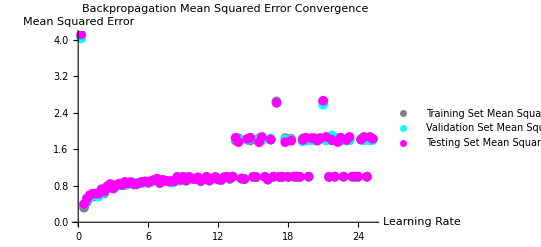

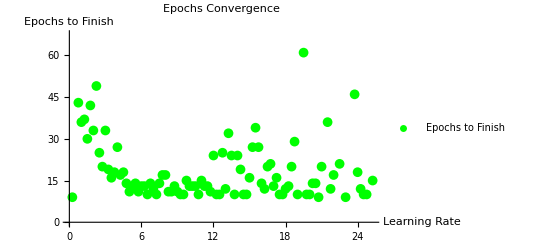

```mathematica
epochsToFinish = {9,82,43,36,37,30,42,33,49,25,20,33,19,16,18,27,17,18,14,11,13,14,11,13,13,10,14,12,10,14,17,17,11,11,13,11,10,10,15,13,13,13,10,15,13,13,11,24,10,10,25,12,32,24,10,24,19,10,10,16,27,34,27,14,12,20,21,13,16,10,10,12,13,20,29,10,92,61,10,10,14,14,9,20,139,36,12,17,93,21,189,9,1000,98,46,18,12,10,10,1000,15};
trainingSetAccuracies = {0.08992805755395683,0.8057553956834532,0.7032374100719424,0.6097122302158273,0.591726618705036,0.5737410071942446,0.5593525179856115,0.4982014388489209,0.5233812949640287,0.38669064748201437,0.35071942446043164,0.40827338129496404,0.32194244604316546,0.2589928057553957,0.26618705035971224,0.29676258992805754,0.22841726618705036,0.21402877697841727,0.2517985611510791,0.23381294964028776,0.22122302158273383,0.24820143884892087,0.16546762589928057,0.2392086330935252,0.20503597122302158,0.14928057553956833,0.17805755395683454,0.15467625899280577,0.07553956834532374,0.1528776978417266,0.14388489208633093,0.18884892086330934,0.20503597122302158,0.09352517985611511,0.16366906474820145,0.08093525179856115,0.10971223021582734,0.08093525179856115,0.14028776978417265,0.1510791366906475,0.10971223021582734,0.16366906474820145,0.11510791366906475,0.09892086330935251,0.1223021582733813,0.18345323741007194,0.13309352517985612,0.12050359712230216,0.08273381294964029,0.10251798561151079,0.10611510791366907,0.09892086330935251,0.0683453237410072,0.10251798561151079,0.07913669064748201,0.09352517985611511,0.14388489208633093,0.09172661870503597,0.10251798561151079,0.08093525179856115,0.09892086330935251,0.07913669064748201,0.09892086330935251,0.10251798561151079,0.11870503597122302,0.09352517985611511,0.08093525179856115,0.07733812949640288,0.09172661870503597,0.09892086330935251,0.07733812949640288,0.09352517985611511,0.08273381294964029,0.07913669064748201,0.09892086330935251,0.09172661870503597,0.08093525179856115,0.10251798561151079,0.07733812949640288,0.09352517985611511,0.09352517985611511,0.08273381294964029,0.08453237410071943,0.09712230215827339,0.09892086330935251,0.09352517985611511,0.10251798561151079,0.09352517985611511,0.07913669064748201,0.10251798561151079,0.10251798561151079,0.0539568345323741,0.09892086330935251,0.09892086330935251,0.10251798561151079,0.09352517985611511,0.09352517985611511,0.09892086330935251,0.08273381294964029,0.09892086330935251,0.09172661870503597};
validationSetAccuracies = {0.11827956989247312,0.7688172043010753,0.6666666666666666,0.6075268817204301,0.5591397849462365,0.5698924731182796,0.5752688172043011,0.4946236559139785,0.478494623655914,0.3709677419354839,0.34408602150537637,0.3870967741935484,0.3602150537634409,0.2903225806451613,0.27956989247311825,0.2956989247311828,0.22580645161290322,0.26881720430107525,0.16666666666666666,0.24193548387096775,0.22043010752688172,0.26881720430107525,0.20430107526881722,0.20967741935483872,0.23655913978494625,0.16129032258064516,0.17204301075268819,0.16129032258064516,0.08602150537634409,0.13440860215053763,0.15591397849462366,0.17204301075268819,0.20967741935483872,0.0967741935483871,0.16666666666666666,0.11290322580645161,0.12903225806451613,0.11290322580645161,0.11290322580645161,0.15053763440860216,0.12903225806451613,0.16129032258064516,0.0967741935483871,0.10215053763440861,0.13978494623655913,0.16129032258064516,0.08064516129032258,0.13978494623655913,0.0967741935483871,0.04838709677419355,0.06451612903225806,0.10215053763440861,0.10752688172043011,0.08064516129032258,0.0913978494623656,0.10215053763440861,0.12365591397849462,0.0967741935483871,0.08064516129032258,0.11290322580645161,0.10752688172043011,0.0913978494623656,0.10215053763440861,0.08064516129032258,0.10752688172043011,0.08064516129032258,0.11290322580645161,0.0913978494623656,0.0967741935483871,0.10215053763440861,0.0913978494623656,0.10215053763440861,0.0967741935483871,0.0913978494623656,0.08064516129032258,0.0967741935483871,0.11290322580645161,0.08064516129032258,0.0913978494623656,0.10215053763440861,0.10215053763440861,0.0967741935483871,0.10215053763440861,0.0967741935483871,0.10215053763440861,0.08064516129032258,0.04838709677419355,0.10215053763440861,0.0913978494623656,0.08064516129032258,0.04838709677419355,0.06989247311827956,0.10215053763440861,0.10215053763440861,0.04838709677419355,0.08064516129032258,0.08064516129032258,0.10215053763440861,0.0967741935483871,0.10215053763440861,0.0967741935483871};
testingSetAccuracies = {0.0846774193548387,0.7419354838709677,0.625,0.592741935483871,0.5,0.5120967741935484,0.5403225806451613,0.4153225806451613,0.5161290322580645,0.34274193548387094,0.32661290322580644,0.4112903225806452,0.3387096774193548,0.2540322580645161,0.2862903225806452,0.22983870967741934,0.1975806451612903,0.18548387096774194,0.2056451612903226,0.23790322580645162,0.22983870967741934,0.2217741935483871,0.14919354838709678,0.2217741935483871,0.16129032258064516,0.0967741935483871,0.11693548387096774,0.1814516129032258,0.0967741935483871,0.12096774193548387,0.14919354838709678,0.1532258064516129,0.14516129032258066,0.0967741935483871,0.14516129032258066,0.0967741935483871,0.125,0.0967741935483871,0.0846774193548387,0.1693548387096774,0.09274193548387097,0.14112903225806453,0.11290322580645161,0.06451612903225806,0.125,0.14919354838709678,0.08064516129032258,0.0846774193548387,0.10483870967741936,0.0967741935483871,0.0967741935483871,0.06451612903225806,0.08064516129032258,0.07258064516129033,0.12096774193548387,0.07661290322580645,0.1693548387096774,0.0846774193548387,0.07258064516129033,0.0967741935483871,0.0846774193548387,0.12096774193548387,0.06451612903225806,0.07258064516129033,0.10887096774193548,0.09274193548387097,0.0967741935483871,0.12096774193548387,0.0846774193548387,0.06451612903225806,0.12096774193548387,0.07661290322580645,0.10483870967741936,0.12096774193548387,0.08064516129032258,0.0846774193548387,0.0967741935483871,0.07258064516129033,0.10887096774193548,0.07661290322580645,0.07661290322580645,0.10483870967741936,0.10080645161290322,0.06854838709677419,0.06451612903225806,0.09274193548387097,0.0967741935483871,0.07661290322580645,0.12096774193548387,0.07258064516129033,0.0967741935483871,0.05241935483870968,0.06451612903225806,0.06451612903225806,0.0967741935483871,0.09274193548387097,0.09274193548387097,0.06451612903225806,0.10483870967741936,0.06451612903225806,0.0846774193548387};
trainingSetMse = {4.077624107623755,0.31983255544461814,0.45094769190397793,0.5502835725865755,0.5614209485058094,0.5792855295045657,0.5837323348197929,0.635328908427374,0.6340472148688187,0.754697394565554,0.7933539328308206,0.7445160482564556,0.7826999202730905,0.8218409107111164,0.8106002050856153,0.8142668349625484,0.8413532137965356,0.8601463518368861,0.8254219866560905,0.8436762821294295,0.8708701045950985,0.8602552155617655,0.8935313511852749,0.8611727708574219,0.8883808864901841,0.9131585528201469,0.9362816461570579,0.8765475037015206,0.9242511538525431,0.9066584769227396,0.8972717340446026,0.8713091997717112,0.8913006379983833,0.9929069242214165,0.9145000498461731,0.9965096003040614,0.9145833826020574,0.9947495279082545,0.9534956043887681,0.9461205014895123,0.9799174186296242,0.8961138207251054,0.9398227598810157,0.9940951771163814,0.9130770004406854,0.9528470319431139,0.9886883161785517,0.9366325911103767,0.9284113770885161,0.9857236106469834,0.9970025222679211,0.9508189842432897,0.9996234765990154,1.7921020581377785,1.841506297669384,0.9569019840492298,0.9462735641975472,1.8156164101669228,1.7942950061638625,0.9965654887505854,0.9918869340507741,1.8386970464425754,1.8021014223547922,0.9977245126903499,0.9353468336489594,1.8127540833367068,0.9990168527377007,2.651050864600815,0.9956905934312398,0.9957883348759635,1.845041658943803,0.9956197069480516,1.8315684593802954,0.999901146690201,0.9999508818787227,0.9951112083100315,1.8377739217353373,1.794823784357522,0.9999258911054927,1.8129312208561652,1.8086001679399877,1.8340686439188378,1.847411953678445,2.641601140990843,1.8021410747011384,0.9958252283268062,1.7949097048955758,0.9999752305124097,1.8416957781898056,1.7948962639255608,0.9999500538691112,1.8196411836737552,1.8021582552762103,0.9999343982271629,0.9999418874095154,0.9999706974391225,1.8128116909368994,1.802095672378607,0.999381986270224,1.8021582733307964,1.8165220506642439};
validationSetMse = {4.030206342592576,0.3914123286845878,0.5064214211739595,0.5603774011719979,0.5841263730623588,0.6089141497622588,0.5658946325969021,0.6748354150093657,0.6530306144780481,0.7544026561038736,0.8174681132565393,0.7597967240071586,0.7894983231270568,0.8209683463781878,0.8172362354804972,0.8226815433084337,0.8397773838705276,0.8475846462308769,0.8688509976413582,0.8493254754542918,0.873554038992931,0.8629745760641442,0.8893760964056301,0.8676853049189528,0.8867556647811992,0.9122996211170382,0.9285055153376496,0.8773119009350955,0.9201436292919981,0.91158144628662,0.9019387358726021,0.8792753073987416,0.8885837417714543,0.9928031808035849,0.9210531010539053,0.9952600782920171,0.9099908115521181,0.9938950029913868,0.9585272393312981,0.9484124119287053,0.9753577457298718,0.9024715771443351,0.9489772430232055,0.9946491275970677,0.9116426222163032,0.9552885463376871,0.9930913360386487,0.9356982779120838,0.92633103447785,0.9877327380905765,0.9930071425141336,0.9520997025344693,0.9992566965335896,1.835932494274872,1.8169224770047225,0.9552113941597619,0.955848893756494,1.8057477843056093,1.8380976465876453,0.9961350126529617,0.9907236043508597,1.8146304548224983,1.7956570519876385,0.998228646178732,0.937744205930785,1.8384708775433147,0.9987128252017434,2.623641045223913,0.9954089582446594,0.9967446348489597,1.8169144991825352,0.994868088151229,1.8031853438015415,0.9998873073381739,0.9999276849448931,0.9948864596825596,1.7737621078198866,1.838507089482336,0.9999290380038648,1.7956845036637186,1.7914911011521706,1.8059153677035966,1.836864977281749,2.5783617349553425,1.795683248491073,0.9959641366162234,1.9031656936883168,0.9999729886047338,1.817173478822125,1.838626856265946,0.9999770586696285,1.7916538744133839,1.79569890661855,0.9999362684275004,0.9999712520604556,0.9999769694547455,1.8385481648224042,1.795629464994314,0.9992149141588654,1.7956989246818165,1.80643250362657};
testingSetMse = {4.117248764508888,0.3977902019138152,0.5249322597991334,0.5947762920131386,0.6266357479520565,0.6284097522111339,0.6273918113819508,0.725208687096686,0.6777741199231498,0.7929121554451504,0.839315098561412,0.7396801120430827,0.8136290253746163,0.846745808706633,0.8180541343935184,0.8867354781453693,0.8518315503169629,0.8826184236511757,0.8504098752251812,0.8349669073773827,0.862477399825238,0.8896024435951896,0.8934569611016338,0.8725412239682856,0.9052180689333673,0.9293745887711621,0.9571012252070089,0.8585727617234259,0.9287692824631235,0.9121717108404384,0.8980135500672101,0.9048103353150845,0.9012473300298526,0.9929062393498488,0.9329295507202636,0.9957454820073661,0.9141255899012448,0.9932339536649658,0.9626230134436727,0.9442627339466271,0.9850210355523881,0.9099951199852303,0.9455986046759262,0.9964458654782893,0.9155257809562237,0.9590956659318782,0.9921883545407754,0.9437555095598575,0.9273798268647243,0.9848955332976927,0.9977797324959878,0.9595875391395112,0.9995954864537395,1.8530182042046568,1.7579431076291672,0.9609429460020238,0.9467127059350205,1.8297548915320314,1.8543268106844675,0.995486556468638,0.9908960074443446,1.7549236011969946,1.8709246222779992,0.9983853544887258,0.9371536639547164,1.8143413289422134,0.9987696688796567,2.6209406442006054,0.9963714240174453,0.997124164426853,1.7578071217710098,0.996102590175752,1.7872172394392463,0.9998519828347332,0.9999987792021607,0.995587276489654,1.806215731276503,1.8546757165597736,0.9999129821880325,1.846762124274757,1.8435776031429993,1.7896831454599464,1.839782363911628,2.6658949577192823,1.8709530818189901,0.9956130880621821,1.80637641013409,0.9999794863694293,1.7580416524953475,1.8547782531220733,0.9999534741216813,1.8041816133827195,1.8709677339328774,0.9999560028969874,0.9999471943428591,0.9999728053167632,1.8144044252583293,1.8708729671005413,0.9990060263756605,1.870967741900666,1.8306227362124847};
range = Range[Length[trainingSetAccuracies]] * 0.25;

(*ListPlot[{Transpose[{range,1-trainingSetAccuracies}],Transpose[{range,1-validationSetAccuracies}],Transpose[{range,1-testingSetAccuracies}],Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}],Transpose[{range,testingSetMse}]}, AxesLabel->{Style["Learning Rate", Black],Style["Value", Black]}, PlotLabel->Style["Backpropagation Convergence", Black], PlotStyle->{Blue, Red, Green, Gray, Cyan, Magenta},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Misclassification", "Validation Set Misclassification","Testing Set Misclassification", "Training Set Mean Squared Error", "Validation Set Mean Squared Error", "Testing Set Mean Squared Error"}]*)

ListPlot[{Transpose[{range,trainingSetAccuracies}],Transpose[{range,validationSetAccuracies}],Transpose[{range,testingSetAccuracies}]}, AxesLabel->{Style["Learning Rate", Black],Style["Classified Correctly", Black]}, PlotLabel->Style["Backpropagation Accuracy Convergence", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Validation Set Accuracy", "Testing Set Accuracy"}]

ListPlot[{Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}],Transpose[{range,testingSetMse}]}, AxesLabel->{Style["Learning Rate", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["Backpropagation Mean Squared Error Convergence", Black], PlotStyle->{Gray, Cyan, Magenta},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Mean Squared Error", "Validation Set Mean Squared Error", "Testing Set Mean Squared Error"}]

ListPlot[Transpose[{range,epochsToFinish}], AxesLabel->{Style["Learning Rate", Black],Style["Epochs to Finish", Black]}, PlotLabel->Style["Epochs Convergence", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Epochs to Finish"}]
```

### Part 4

Below are plots showing the optimal amount of nodes in the hidden layer. As shown, the optimal number seems to be around 80. Interestingly, the number of epochs required to finish are very sporadic but show much the same thing: that there a local maximum/minimum around 80 hidden layer nodes. The likely cause of the decrease in required epochs at 128 hidden-layer nodes is likely because of the random-nature of the starting criteria. Each node has randomized weights and the more nodes that are initialized the more likely it is that some of those weights correspond to the natural weight of the system. After a few epochs, these weights will start to be favored by the system.

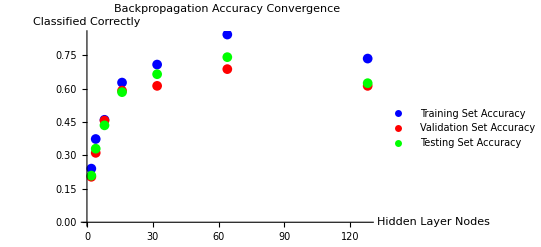

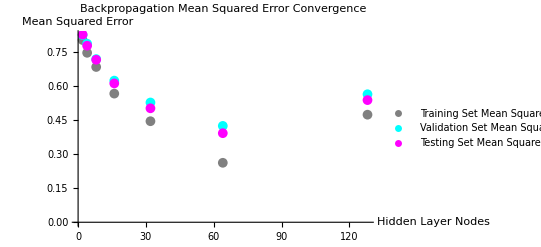

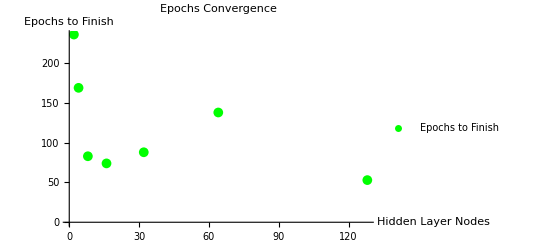

```mathematica
epochsToFinish = {236,169,83,74,88,138,53};
trainingSetAccuracies = {0.24100719424460432,0.37410071942446044,0.460431654676259,0.6276978417266187,0.7086330935251799,0.8435251798561151,0.7356115107913669};
validationSetAccuracies = {0.20430107526881722,0.3118279569892473,0.45698924731182794,0.5913978494623656,0.6129032258064516,0.6881720430107527,0.6129032258064516};
testingSetAccuracies = {0.20967741935483872,0.33064516129032256,0.43548387096774194,0.5846774193548387,0.6653225806451613,0.7419354838709677,0.625};
trainingSetMse = {0.8024884583317398,0.7462462768469159,0.6837699726612526,0.566533185730693,0.4449472884515421,0.26185150380468825,0.47370619880056847};
validationSetMse = {0.824321191903507,0.7862196538515609,0.7185184158130572,0.6237612770780975,0.5273667823703068,0.4243452879582946,0.5637124383157393};
testingSetMse = {0.826628010436207,0.7775112797403259,0.7155381262894088,0.6114397246692522,0.5018420744472569,0.392228529527198,0.5379073583747477};
range = 2^Range[Length[trainingSetAccuracies]] ;

(*ListPlot[{Transpose[{range,1-trainingSetAccuracies}],Transpose[{range,1-validationSetAccuracies}],Transpose[{range,1-testingSetAccuracies}],Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}],Transpose[{range,testingSetMse}]}, AxesLabel->{Style["Hidden Layer Nodes", Black],Style["Value", Black]}, PlotLabel->Style["Backpropagation Convergence", Black], PlotStyle->{Blue, Red, Green, Gray, Cyan, Magenta},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Misclassification", "Validation Set Misclassification","Testing Set Misclassification", "Training Set Mean Squared Error", "Validation Set Mean Squared Error", "Testing Set Mean Squared Error"}]*)

ListPlot[{Transpose[{range,trainingSetAccuracies}],Transpose[{range,validationSetAccuracies}],Transpose[{range,testingSetAccuracies}]}, AxesLabel->{Style["Hidden Layer Nodes", Black],Style["Classified Correctly", Black]}, PlotLabel->Style["Backpropagation Accuracy Convergence", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Validation Set Accuracy", "Testing Set Accuracy"}]

ListPlot[{Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}],Transpose[{range,testingSetMse}]}, AxesLabel->{Style["Hidden Layer Nodes", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["Backpropagation Mean Squared Error Convergence", Black], PlotStyle->{Gray, Cyan, Magenta},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Mean Squared Error", "Validation Set Mean Squared Error", "Testing Set Mean Squared Error"}]

ListPlot[Transpose[{range,epochsToFinish}], AxesLabel->{Style["Hidden Layer Nodes", Black],Style["Epochs to Finish", Black]}, PlotLabel->Style["Epochs Convergence", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Epochs to Finish"}]
```

### Part 5

Below shows the momentum value as it changes between the values of 0 and 1.2. As shown, there is not much difference and all the variation is likely just due to stochastic reasons. I tested values greater than 1.2 but all of these values required more than 1000 epochs to converge to the data (if they converged at all). It threw off the plots and so they are not included here. It is surprising that such a large jump occurs in the convergence of the algorithm between the values of 1.2 and 1.4 (where the convergence blew up).

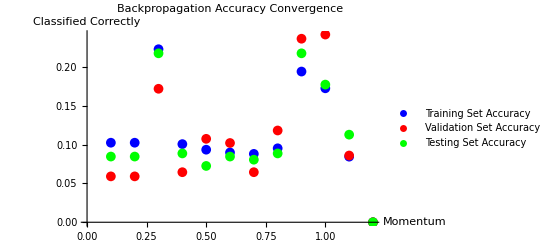

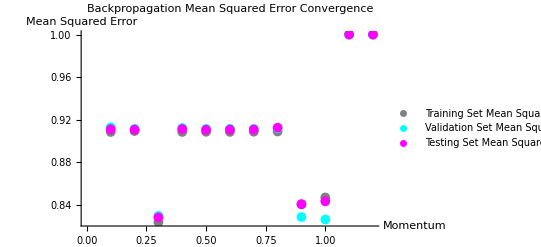

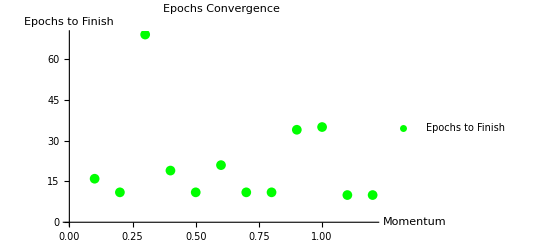

```mathematica
epochsToFinish = {16,11,69,19,11,21,11,11,34,35,10,10,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}[[1;;12]];
trainingSetAccuracies = {0.10251798561151079,0.10251798561151079,0.22302158273381295,0.10071942446043165,0.09352517985611511,0.08992805755395683,0.08812949640287769,0.09532374100719425,0.19424460431654678,0.17266187050359713,0.08453237410071943,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0}[[1;;12]];
validationSetAccuracies = {0.05913978494623656,0.05913978494623656,0.17204301075268819,0.06451612903225806,0.10752688172043011,0.10215053763440861,0.06451612903225806,0.11827956989247312,0.23655913978494625,0.24193548387096775,0.08602150537634409,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0}[[1;;12]];
testingSetAccuracies = {0.0846774193548387,0.0846774193548387,0.21774193548387097,0.08870967741935484,0.07258064516129033,0.0846774193548387,0.08064516129032258,0.08870967741935484,0.21774193548387097,0.1774193548387097,0.11290322580645161,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0}[[1;;12]];
trainingSetMse = {0.9084566611937508,0.9093620851907219,0.8236471675447764,0.9084968535267653,0.9086458689133371,0.9085556926030615,0.9087081317542057,0.908920323831692,0.840526948686712,0.8469598665697892,1.0,1.0,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN}[[1;;12]];
validationSetMse = {0.9128990349007392,0.911488100316454,0.8296495677018004,0.912180528727306,0.9113838503863844,0.9114884709800833,0.911360388704502,0.9118504637867227,0.8285987060645438,0.8262079914801279,1.0,1.0,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN}[[1;;12]];
testingSetMse = {0.9110362458793698,0.9106764590512139,0.8282104319301907,0.9112703487983423,0.9105521004822454,0.9106792171165441,0.9107742580463757,0.9124960009236208,0.8406144928245933,0.8432809310209833,1.0,1.0,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN}[[1;;12]];
range = Range[Length[trainingSetAccuracies]]*0.1 ;

(*ListPlot[{Transpose[{range,1-trainingSetAccuracies}],Transpose[{range,1-validationSetAccuracies}],Transpose[{range,1-testingSetAccuracies}],Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}],Transpose[{range,testingSetMse}]}, AxesLabel->{Style["Momentum", Black],Style["Value", Black]}, PlotLabel->Style["Backpropagation Convergence", Black], PlotStyle->{Blue, Red, Green, Gray, Cyan, Magenta},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Misclassification", "Validation Set Misclassification","Testing Set Misclassification", "Training Set Mean Squared Error", "Validation Set Mean Squared Error", "Testing Set Mean Squared Error"}]*)

ListPlot[{Transpose[{range,trainingSetAccuracies}],Transpose[{range,validationSetAccuracies}],Transpose[{range,testingSetAccuracies}]}, AxesLabel->{Style["Momentum", Black],Style["Classified Correctly", Black]}, PlotLabel->Style["Backpropagation Accuracy Convergence", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Accuracy", "Validation Set Accuracy", "Testing Set Accuracy"}]

ListPlot[{Transpose[{range,trainingSetMse}],Transpose[{range,validationSetMse}],Transpose[{range,testingSetMse}]}, AxesLabel->{Style["Momentum", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["Backpropagation Mean Squared Error Convergence", Black], PlotStyle->{Gray, Cyan, Magenta},PlotMarkers-> {●,10}, PlotLegends->{"Training Set Mean Squared Error", "Validation Set Mean Squared Error", "Testing Set Mean Squared Error"}]

ListPlot[Transpose[{range,epochsToFinish}], AxesLabel->{Style["Momentum", Black],Style["Epochs to Finish", Black]}, PlotLabel->Style["Epochs Convergence", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Epochs to Finish"}]
```

### Part 6

For my project I attempted to add another hidden layer to the neural net with nodes updated in much the same way as the other algorithm. I tested it on the same file as before (vowels) and found a very similar convergence. Essentially, adding a second layer was no more effective than adding the equivalent number of nodes to the single-layer model. Below are the convergence statistics for both algorithms. As always, each algorithm used a 75/25 training/testing data split with a stopping criteria that would trigger when 10 successive epochs were presented with no improvement above the BSSF.

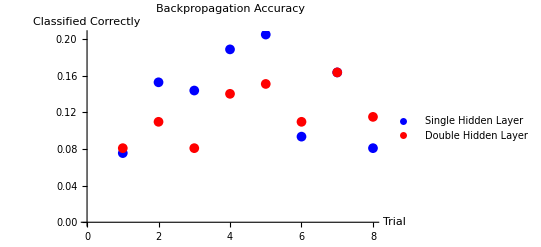

The average accurracy for the algorithm with one layer was 0.13804

The average accurracy for the algorithm with two layers was 0.11893

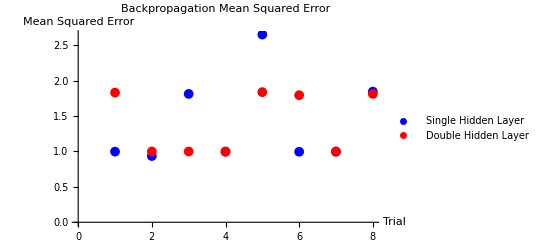

The average mean squared error for the algorithm with one layer was 1.40405

The average mean squared error for the algorithm with two layers was 1.409

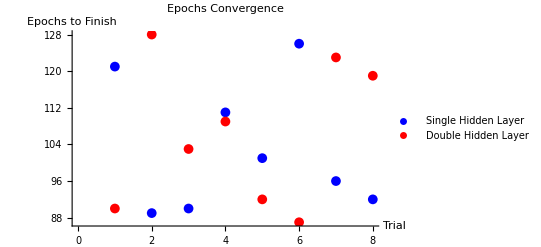

The average number of epochs to finish for the algorithm with one layer was 103.25

The average number of epochs to finish for the algorithm with two layers was 106.375

```mathematica
epochsToFinishMod1 = {121, 89, 90, 111, 101, 126, 96, 92};
epochsToFinishMod2 = {90, 128, 103, 109, 92, 87, 123, 119};
mod1Accuracies = {0.07553956834532374,0.1528776978417266,0.14388489208633093,0.18884892086330934,0.20503597122302158,0.09352517985611511,0.16366906474820145,0.08093525179856115};
mod2Accuracies = {0.08093525179856115,0.10971223021582734,0.08093525179856115,0.14028776978417265,0.1510791366906475,0.10971223021582734,0.16366906474820145,0.11510791366906475};
mod1Mse = {0.9977245126903499,0.9353468336489594,1.8127540833367068,0.9990168527377007,2.651050864600815,0.9956905934312398,0.9957883348759635,1.845041658943803};
mod2Mse = {1.8315684593802954,0.999901146690201,0.9999508818787227,0.9951112083100315,1.8377739217353373,1.794823784357522,0.9999258911054927,1.8129312208561652};
range = Range[Length[epochsToFinishMod1]] ;

ListPlot[{Transpose[{range,mod1Accuracies}],Transpose[{range,mod2Accuracies}]}, AxesLabel->{Style["Trial", Black],Style["Classified Correctly", Black]}, PlotLabel->Style["Backpropagation Accuracy", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Single Hidden Layer", "Double Hidden Layer"}]

Print["The average accurracy for the algorithm with one layer was ",N[Mean[mod1Accuracies]]]
Print["The average accurracy for the algorithm with two layers was ",N[Mean[mod2Accuracies]]]

ListPlot[{Transpose[{range,mod1Mse}],Transpose[{range,mod2Mse}]}, AxesLabel->{Style["Trial", Black],Style["Mean Squared Error", Black]}, PlotLabel->Style["Backpropagation Mean Squared Error", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Single Hidden Layer", "Double Hidden Layer"}]

Print["The average mean squared error for the algorithm with one layer was ",N[Mean[mod1Mse]]]
Print["The average mean squared error for the algorithm with two layers was ",N[Mean[mod2Mse]]]

ListPlot[{Transpose[{range,epochsToFinishMod1}],Transpose[{range,epochsToFinishMod2}]}, AxesLabel->{Style["Trial", Black],Style["Epochs to Finish", Black]}, PlotLabel->Style["Epochs Convergence", Black], PlotStyle->{Blue, Red, Green},PlotMarkers-> {●,10}, PlotLegends->{"Single Hidden Layer", "Double Hidden Layer"}]

Print["The average number of epochs to finish for the algorithm with one layer was ",N[Mean[epochsToFinishMod1]]]
Print["The average number of epochs to finish for the algorithm with two layers was ",N[Mean[epochsToFinishMod2]]]
```